```mathematica
Fsin[n_]:=Sin[n*θ]
Fcos[m_]:=Cos[m*θ]
```

```mathematica
Integrate[Fsin[1]*Fcos[1],{θ,0,2*Pi}]
```

0

```mathematica
Integrate[Fsin[2]*Fsin[2],{θ,-Pi,Pi}]//FullSimplify
```

π

```mathematica
Integrate[Fsin[3]*Fsin[2],{θ,-Pi,Pi}]
```

0

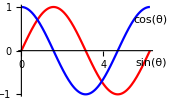

```mathematica
Plot[{Fsin[1],Fcos[1]},{θ,0,2*Pi},PlotStyle->{Red,Blue},PlotLabels->Placed[{Fsin[1],Fcos[1]},{{Scaled[1],Below}}]]
```

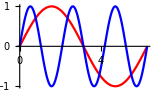

```mathematica
Plot[{Fsin[1],Fsin[3]},{θ,0,2*Pi},PlotStyle->{Red,Blue}]
```

```mathematica
Integrate[Fsin[1]*Fsin[3],{θ,0,2*Pi}]
```

0

Integrate::idiv: Integral of 12+(13 x)/2-x^2 does not converge on {-∞,∞}.

∫_(-∞)^∞ (2-x/4) (6+4 x)ⅆx

```mathematica
FunctionDomain[54 Null,{}]
```

True